```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

\\wsl$\Ubuntu\home\pjoot\project\figures\GAelectrodynamics

```mathematica
<<MaTeX`
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor,txfonts},\definecolor{BlueDarker}{HTML}{0000AA},\definecolor{RedDarker}{HTML}{AA0000},\definecolor{PurpleDarker}{HTML}{550055},\definecolor{OrangeDarker}{HTML}{AA5500},\definecolor{GreenDarker}{HTML}{00AA00}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→16,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

{1/(√5),2/(√5)}

-Graphics3D-

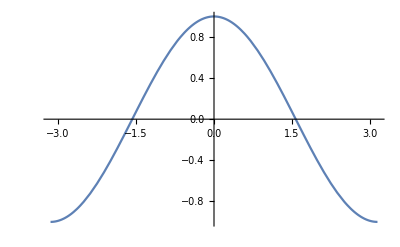

```mathematica
ClearAll[o, f, r, p]

o = {0,0, 0};
f[u_] :={
-(1-u^4) Sin[u]/(Pi^2)/2
,1.5(1/2+(1+ u^2) Cos[u]/(Pi^2))
(*, (1-u^2) Sin[u]/(Pi)*)
, Sin[u]
};
(*g[u_] := f[u/Pi]*)
r= 1.3{-1, 1};
u0 = -Pi/4;
u1 =  4Pi;
plot =ParametricPlot3D[ f[u], {u, u0,u1}
, AspectRatio-> 1
, PlotTheme->"ThickLines"
, PlotRange->{r,r,r}
, Axes -> None
];
df[u_] := D[f[x],x] /. x -> u;
{1,2}// Normalize
Show[{plot,
Graphics3D[{
Red,Arrowheads[0.05],
Table[Arrow[Tube[{f[u], f[u] + ((df[u](*// Normalize*))/2)}]],{u,u0,u1,(u1-u0)/20}] 
}
]
}]


(*Plot[Evaluate@g[x], {x,-1,1}]*)
(*Plot[Evaluate@f[x], {x,-Pi,Pi}, PlotLabels->Automatic]*)
```